# Spectral Lags in Very High Energy Emission of GRBs

## Model

### Parameters

```mathematica
universe={Hobs_,Ωm_};
```

```mathematica
population={density0_,index_,zc_};
```

```mathematica
burst={γ_,η0_,r0_,n_,ω0_,θ0_,k_,α_};
```

```mathematica
observer={detectorArea_,z_,χ_};
```

### Relativity

```mathematica
v[γ_]:=√(1-1/γ^2);
```

### Cosmology

```mathematica
ΩΛ[Ωm_]:=1-Ωm;
```

```mathematica
distance[universe,z_]:=1/Hobs √(1/ΩΛ[Ωm])((1+z)Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm](1+z)^3]-Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm]]);
```

```mathematica
photonSphereArea[universe_,z_]:=4π distance[universe,z]^2;
```

```mathematica
burstsSphereArea[universe_,z_]:=(4π distance[universe,z]^2)/(1+z)^2;
```

```mathematica
shellVolumePerRedshift[universe,z_]:=(4π distance[{Hobs,Ωm},z]^2)/(1+z)^3 1/(Hobs √(Ωm(1+z)^3+ΩΛ[Ωm]));
```

### Light curve

```mathematica
i[burst,z_,χ_,ω_,θ_,ϕ_]:=
If[ω==∞,
0,
1/(2k)ω(ω/ω0)^α ExpIntegralE[(α+1)/(2k)+1,(θ/θ0)^2(ω/ω0)^(-2k)(v[γ]γ(1+z)(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ]))^(-2k)]
];
```

```mathematica
j[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z))^3 π/(n Sin[(3π)/n]),
τ^3/3 Hypergeometric2F1[1,3/n,(n+3)/n,-(τ/(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z)))^n]
];
```

```mathematica
p[universe_,burst,observer,{τ1_,τ2_},{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
detectorArea/photonSphereArea[universe,z](2η0)/(v[γ]γ(1+z))^(2-α)(NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])(j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ]),{θ,0,χ},{ϕ,0,π}]+NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])(j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ]),{θ,χ,∞},{ϕ,0,π}])
];
```

### Duration

```mathematica
Options[duration]={part->0.99};
duration[universe_,burst,observer,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,observerValues,p∞,precision},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
observerValues={detectorArea,z,χ};
p∞=p[universe,burstValues,observerValues,{0.,∞},{ω1,ω2}];
pi[τ_?NumberQ]:=p[universe,burstValues,observerValues,{0.,τ},{ω1,ω2}];
τ/.FindRoot[pi[τ]-OptionValue[part]p∞,{τ,r0/γ^2(1.+z)}]
];
```

### Stretching factor

```mathematica
jτ[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
0,
τ^2/(1+((2τ)/(r0 (1+z) (-2+2/v[γ]+θ^2+χ^2-2 θ χ Cos[ϕ])))^n)
];
```

```mathematica
pτ[universe_,burst,observer,τ_,{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
detectorArea/photonSphereArea[universe,z](2η0)/(v[γ]γ(1+z))^(2-α)(NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ],{θ,0,χ},{ϕ,0,π}]+NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ],{θ,χ,∞},{ϕ,0,π}])
];
```

```mathematica
Options[κ]={δ->0.01,accurateQ->True};
κ[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{p12∞,p23∞,diff,diffτ,δτ,τmiddle,τend,κmin,κmax,minDifference,maxDifference,diffDifference,precision,accQ},
p12∞=p[universe,burst,observer,{0.,∞},{ω1,ω2}];
p23∞=p[universe,burst,observer,{0.,∞},{ω2,ω3}];
diff[τ_?NumberQ,κ_?NumberQ]:=p[universe,burst,observer,{0.,τ},{ω1,ω2}]/(p12∞)-p[universe,burst,observer,{0.,κ τ},{ω2,ω3}]/(p23∞);
diffτ[τ_?NumberQ,κ_?NumberQ]:=pτ[universe,burst,observer,τ,{ω1,ω2}]/(p12∞)-κ pτ[universe,burst,observer,κ τ,{ω2,ω3}]/(p23∞);
accQ=OptionValue[accurateQ];
If[TrueQ[accQ],
τend=duration[universe,burst,observer,{ω1,ω3}];
δτ=OptionValue[δ]τend;
maxDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]>0,
If[diff[τend,κ]>0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,zero-δτ}];
];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
];
minDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]<0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
If[diff[τend,κ]<0,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,zero+δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
]
];
κmin=κi/.FindRoot[diff[δτ,κi],{κi,1.}];
κmax=κi/.FindRoot[diff[τend,κi],{κi,1.}];
diffDifference[κ_?NumberQ]:=maxDifference[κ][[2]]+minDifference[κ][[2]];
κi/.FindRoot[diffDifference[κi],{κi,κmin,κmax}]
,
τmiddle=duration[universe,burst,observer,{ω1,ω3},part->0.5];
κi/.FindRoot[diff[τmiddle,κi],{κi,1.}]
]
];
```

```mathematica
SetSharedFunction[κStoredValues];
Options[κCache]={δ->0.01,accurateQ->True};
κCache[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{},
If[Not[NumberQ[κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]]],κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]=κ[universe,burst,observer,{ω1,ω2,ω3},δ->OptionValue[δ],accurateQ->OptionValue[accurateQ]]];
κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]
];
```

```mathematica
κSave[]:=DumpSave["kappa.mx",κStoredValues];
```

```mathematica
κLoad[]:=If[FileExistsQ["kappa.mx"],<<"kappa.mx"];
```

### Total Energy

```mathematica
energy[burst,ω1_]:=(16 π^3)/(3n(-2k-α-2)Sin[(3π)/n])γ^(-2k-α)(1-1/(4 γ^2))η0 r0^3 θ0^2 ω0^(-2k-α)/ω1^(-2k-α-2);
```

### Distribution of stretching factors

#### Algorithms

```mathematica
Options[zmax]={minParticles->10};
zmax[universe_,burst_,detectorArea_,χ_,{ω1_,ω2_},OptionsPattern[]]:=Block[{int,z1,z2},
int[z_?NumberQ]:=p[universe,burst,{detectorArea,z,χ},{0.,∞},{ω1,ω2}]-OptionValue[minParticles];
z1=1;
While[int[z1]<0,z1/=2.];
z2=1;
While[int[z2]>0,z2*=2.];
z/.FindRoot[int[z],{z,z1,z2}]
];
```

```mathematica
Options[χmax]={minParticles->10};
χmax[universe_,burst,detectorArea_,z_,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,int,χ0},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
int[χ_?NumberQ]:=p[universe,burstValues,{detectorArea,z,χ},{0.,∞},{ω1,ω2}]-OptionValue[minParticles];
If[int[0]<0,
Return[0],
χ0=1/γ;
While[int[χ0]>0,χ0*=2.;];
];
χ/.FindRoot[int[χ],{χ,0,χ0}]
];
```

```mathematica
burstDensity[population,z_]:=density0(1+z)^index Exp[-z/zc];
```

```mathematica
phaseVolume[universe_,population_,{z1_?NumberQ,z2_?NumberQ}]:=NIntegrate[shellVolumePerRedshift[universe,z]burstDensity[population,z],{z,z1,z2}];
```

```mathematica
randomRedshift[universe_,population_,{z1_,z2_}]:=Block[{total,chosenVolume},
total=phaseVolume[universe,population,{z1,z2}];
chosenVolume=RandomReal[total];
z/.FindRoot[phaseVolume[universe,population,{z1,z}]-chosenVolume,{z,z1,z2}]
];
```

```mathematica
randomAngle[{χ1_,χ2_}]:=√RandomReal[{χ1^2,χ2^2}];
```

```mathematica
inRegionQ[region_,point_]:=Block[{i},
For[i=1,i≤Length[region],i++,
If[region[[i]][[1]]≤point[[1]]&&region[[i]][[2]]≤point[[2]],Return[True]];
];
Return[False];
];
```

```mathematica
addToRegion[region_,point_]:=Block[{i,j},
For[i=1,i≤Length[region],i++,
If[region[[i]][[1]]>point[[1]],
If[i==1||region[[i-1]][[2]]>point[[2]],
For[j=i,j≤Length[region]&&region[[j]][[2]]>point[[2]],j++];
Return[Insert[Drop[region,{i,j-1}],point,i]];
,
Return[region];
];
];
];
If[Length[region]==0||region[[Length[region]]][[2]]>point[[2]],
Return[Insert[region,point,Length[region]+1]];
,
Return[region];
];
];
```

```mathematica
Options[plotRegion]={axesOrigin->Automatic};
plotRegion[region_,range_,OptionsPattern[]]:=Block[{plotPoints},
If[Length[region]==0,Return[ListPlot[{Missing},PlotRange->range]]];
plotPoints=Flatten[Table[{region[[i]],{region[[i+1]][[1]],region[[i]][[2]]}},{i,1,Length[region]-1}],1];
AppendTo[plotPoints,region[[Length[region]]]];
AppendTo[plotPoints,{range[[1]][[2]],region[[Length[region]]][[2]]}];
ListPlot[plotPoints,PlotStyle->LightRed,Joined->True,PlotRange->range,Filling->Top,FillingStyle->LightRed,AxesOrigin->OptionValue[axesOrigin]]
];
```

```mathematica
Options[κSample]={accurateQ->True,randomSeed->"Gamma Rays",zmin->0.1,minParticles->10,monitorQ->False};
κSample[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},n_,OptionsPattern[]]:=Block[{
z2,χ2,it,zc,χc,pointsChosen,pointsStarted,pointsCompleted,result,region,κValues,curκ,
text,plot2D,plot3D,plotCDF,print
},
SeedRandom[OptionValue[randomSeed]];
SetSharedVariable[pointsStarted];
SetSharedVariable[pointsCompleted];
SetSharedVariable[κValues];
pointsChosen={};
pointsStarted={};
pointsCompleted={};
κValues={};
region={};
it=0;
If[OptionValue[monitorQ],
print=PrintTemporary[Dynamic[
text=If[it==0,"initializing",
If[Length[pointsStarted]>0,ToString[Length[pointsCompleted]]<>"/"<>ToString[n]<>" κ values computed",
ToString[Length[pointsChosen]]<>"/"<>ToString[n]<>" points chosen"
]
];
plot2D=If[it==0,"[2D plot will be here]",
Show[
plotRegion[region,{{OptionValue[zmin],z2},{0,χ2}}],
ListPlot[{pointsChosen/.{}->Missing,pointsStarted/.{}->Missing,pointsCompleted/.{}->Missing},
PlotStyle->{Blue,Red,Green}]
]
];
plot3D=If[Length[κValues]>0,
ListPointPlot3D[κValues,PlotRange->{{OptionValue[zmin],z2},{0,χ2},Full},ColorFunction->"Rainbow"],
"[3D plot will be here]"
];
plotCDF=If[Length[pointsCompleted]>0,
Plot[CDF[EmpiricalDistribution[Transpose[κValues][[3]]],κi],{κi,0.8Min[Transpose[κValues][[3]]],1.2Max[Transpose[κValues][[3]]]}],
"[cdf will be here]"
];
Grid[{{text},{plot2D,plot3D,plotCDF}}]
]]];
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3},minParticles->OptionValue[minParticles]];
χ2=χmax[universe,burst,detectorArea,OptionValue[zmin],{ω2,ω3},minParticles->OptionValue[minParticles]];
For[it=1,it≤n,it++,
zc=randomRedshift[universe,population,{OptionValue[zmin],z2}];
χc=randomAngle[{0,χ2}];
If[inRegionQ[region,{zc,χc}],it--,
If[p[universe,burst,{detectorArea,zc,χc},{0,∞},{ω2,ω3}]≥10.,
AppendTo[pointsChosen,{zc,χc}];
,
region=addToRegion[region,{zc,χc}];
it--;
];
];
];
κLoad[];
result=ParallelTable[
AppendTo[pointsStarted,{point[[1]],point[[2]]}];
curκ=κCache[universe,burst,Flatten[{detectorArea,point}],{ω1,ω2,ω3},accurateQ->OptionValue[accurateQ]];
AppendTo[pointsCompleted,{point[[1]],point[[2]]}];
AppendTo[κValues,{point[[1]],point[[2]],curκ}];
curκ,{point,pointsChosen},Method->"FinestGrained"];
κSave[];
If[OptionValue[monitorQ],
NotebookDelete[print];
];
UnsetShared[pointsStarted];
UnsetShared[pointsCompleted];
UnsetShared[κValues];
result
];
```

#### Results

```mathematica
mcData=κSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{0.1,1.,∞},600,monitorQ->True];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
mcDataIA=κSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{0.1,1.,∞},1000,monitorQ->True,accurateQ->False];
```

```mathematica
mcData500IA=κSample[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{0.1,1.,∞},1000,monitorQ->True,accurateQ->False];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
κObserved={
{Text["090902B"],{0.600207,1.39668}},
{Text["080916C"],{0.669292,3.51709}},
{Text["090926A"],{1.66697,4.91586}}
};
```

```mathematica
errorBar[{min_,max_},y_,height_,{label_,x_}]:=Graphics[{Black,Line[{{min,y},{max,y}}],Line[{{min,y-height},{min,y+height}}],Line[{{max,y-height},{max,y+height}}],{Black,Inset[label,{x,y},{Right,Bottom}]}}];
```

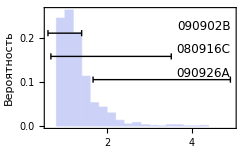

```mathematica
Block[{κ1,κ2,top},
κ1=Min[Transpose[Transpose[κObserved][[2]]][[1]]];
κ2=Max[Transpose[Transpose[κObserved][[2]]][[2]]];
top=Max[HistogramList[mcData][[2]]]/600;
Show[
Histogram[mcData,Automatic,"Probability",Frame->{{True,False},{True,False}},PlotRangePadding->0,FrameLabel->{"Коэффициент растяжения","Вероятность"},LabelStyle->(FontSize->12),PlotRange->{{κ1,1.01κ2},All}],
Table[errorBar[κObserved[[it]][[2]],top(1-0.2it),0.007,{Style[κObserved[[it]][[1]],FontSize->12],κ2}],{it,1,Length[κObserved]}]
]
]
```

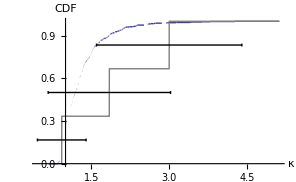

```mathematica
Block[{it},
Show[
Plot[CDF[EmpiricalDistribution[mcData],κi],{κi,0.8Min[mcData],1.2Max[mcData]},AxesLabel->{"κ","CDF"},PlotRange->All],
Plot[CDF[EmpiricalDistribution[Table[Mean[value[[2]]],{value,κObserved}]],κi],{κi,0.8Min[mcData],1.2Max[mcData]},PlotStyle->Gray],
Table[errorBar[κObserved[[it]][[2]],(2it-1)/(2Length[κObserved]),0.01,{"",κObserved[[it]][[2]][[1]]}],{it,1,Length[κObserved]}]
]
]
```

```mathematica
Binomial[35,3] 0.072^3(1-0.072)^(35-3)
```

0.223585

### Very high energy bursts fraction

#### Algorithms

```mathematica
Options[burstFraction]={minParticles->10};
burstFraction[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{z1,z2,int},
z1=zmax[universe,burst,detectorArea,0,{ω1,ω3},minParticles->OptionValue[minParticles]];
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3},minParticles->OptionValue[minParticles]];
int[z_?NumberQ,{ωl_,ωr_}]:=burstDensity[population,z]shellVolumePerRedshift[universe,z] χmax[universe,burst,detectorArea,z,{ωl,ωr}]^2;
NIntegrate[int[z,{ω2,ω3}],{z,0,z2}]/NIntegrate[int[z,{ω1,ω3}],{z,0,z1}]
];
```

#### Results

```mathematica
PrintTemporary[Dynamic[z]];
Timing[burstFraction[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{0.1,1.,∞}]]
```

{3321.83545,0.0720929}

```mathematica
PrintTemporary[Dynamic[z]];
Timing[burstFraction[defaultUniverse[],defaultPopulation[],defaultBurst500[],defaultDetectorArea[],{0.1,1.,∞}]]
```

{3738.33563,0.010223}

### Default Parameters

```mathematica
Options[defaultUniverse]={Hobs->2.*^-18,Ωm->0.317};
defaultUniverse[OptionsPattern[]]:={OptionValue[Hobs],OptionValue[Ωm]};
```

```mathematica
Options[defaultPopulation]={density0->0.655427*^-50,index->3,zc->3.};
defaultPopulation[OptionsPattern[]]:={OptionValue[density0],OptionValue[index],OptionValue[zc]};
```

```mathematica
Options[defaultBurst]={γ->100.,η0->1.*^45,r0->2.*^3,n->6,ω0->1.,θ0->2.5*^-5,k->-1,α->-1};
defaultBurst[OptionsPattern[]]:={OptionValue[γ],OptionValue[η0],OptionValue[r0],OptionValue[n],OptionValue[ω0],OptionValue[θ0],OptionValue[k],OptionValue[α]};
```

```mathematica
defaultDetectorArea[]:=5.563*^-18;
```

```mathematica
Options[defaultObserver]={detectorArea->defaultDetectorArea[],z->1.,χ->0.};
defaultObserver[OptionsPattern[]]={OptionValue[detectorArea],OptionValue[z],OptionValue[χ]};
```

```mathematica
p1∞=p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,∞},{0.1,1.}];
```

```mathematica
p2∞=p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,∞},{1.,∞}];
```

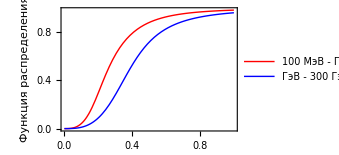

```mathematica
PrintTemporary[Dynamic[t]];
Plot[{
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{0.1,1.}]/(p1∞),
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{1.,∞}]/(p2∞)
},{t,0,1},PlotStyle->{Red,Blue},Frame->{{True,False},{True,False}},FrameLabel->{"Время, с","Функция распределения"},LabelStyle->(FontSize->12),PlotLegends->Placed[{"100 МэВ - ГэВ","ГэВ - 300 ГэВ"},{0.75,0.33}]
]
```